GRÁFICO 2D
Uma função por gráfico

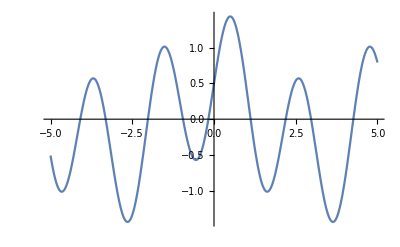

```mathematica
f[x_]:= 1/2 Cos[x]+Sin[3x];
Plot[f[x],{x,-5,5}]
```

Sem declaração antecipada de função

```mathematica
Plot[1/2 Cos[x]+Sin[3x],{x,-5,5}]
```

-Graphics-

Duas ou mais funções por gráfico
com declaração antecipada

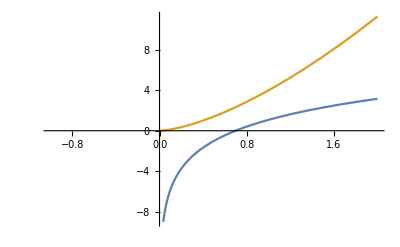

```mathematica
g[x_]:= 3Log[2x]-1;
h[x_]:= 4Sqrt[x^3];
Plot[{g[x],h[x]},{x,-1,2}]
```

Sem declaração antecipada de funções

```mathematica
Plot[{3Log[2x]-1,4Sqrt[x^3]},{x,-1,2}]
```

-Graphics-

GRÁFICO 3D
Uma função por gráfico
COm declaração antecipada de função

```mathematica
s[x_,y_]:= 3(x^2)-2Sin[y];
Plot3D[s[x,y],{x,-1,1},{y,-5,5}]
```

-Graphics3D-

sem declaração antecipada

```mathematica
Plot3D[3x^2-2Sin[y], {x,-1,1},{y,-5,5}]
```

-Graphics3D-

Duas funções por gráfico

```mathematica
a[x_,y_]:=3x+y;
b[x_,y_]:= 2Exp[x^2+Log[y]];
Plot3D[{a[x,y], b[x,y]},{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[{3x+y, 2Exp[x^2 +Log[y]]},{x,-3,3},{y,-3,3}]
```

-Graphics3D-

PERSONALIZAÇÃO DE GRÁFICOS
Funções de entrada

```mathematica
f[x_]:= Sin[x];
g[x_]:=Cos[2x];
```

título do gráfico

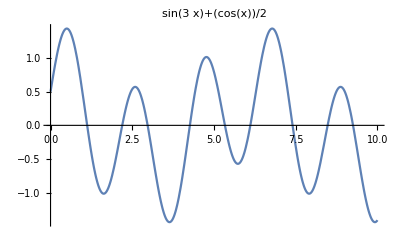

```mathematica
Plot[f[x],{x,0,10},PlotLabel-> f[x]]
```

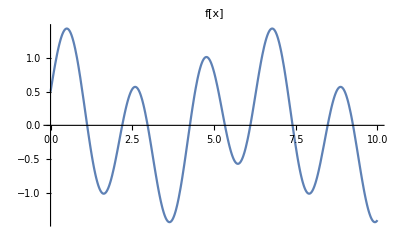

```mathematica
Plot[f[x],{x,0,10},PlotLabel-> "f[x]"]
```

```mathematica
Plot[f[x],{x,0,10},PlotLabel-> f[x], LabelStyle->Directive[Bold,Red]]
```

-Graphics-

```mathematica
Plot[f[x],{x,0,10},PlotLabel-> Style[Framed[f[x]],20, Red]]
```

-Graphics-

```mathematica
Plot[f[x],{x,0,10},PlotLabel-> Style[Framed[f[x]],20, Red, Background->LightGray]]
```

-Graphics-

Nomes dos eixos

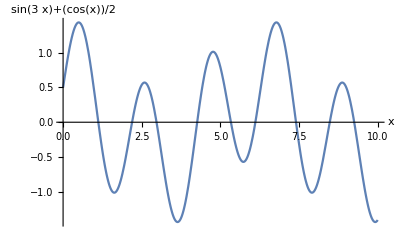

```mathematica
Plot[f[x],{x,0,10},AxesLabel-> {x,f[x]}]
```

```mathematica
Plot[f[x],{x,0,10},AxesLabel-> {x,f[x]}, LabelStyle->Directive[Bold, Darker[Red],12]]
```

-Graphics-

Marcações dos eixos

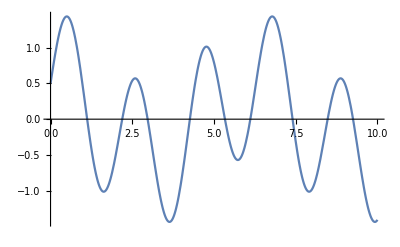

```mathematica
Plot[f[x],{x,0,10},Ticks->Automatic]
```

```mathematica
Plot[f[x],{x,0,10},Ticks->None]
```

-Graphics-

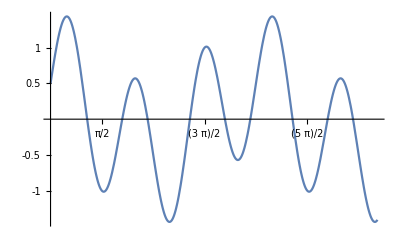

```mathematica
Plot[f[x],{x,0,10},Ticks->{{Pi/2,Pi,3/2 Pi,2Pi,5/2 Pi,3Pi},{-1,-0.5,0.5,1}}]
```

Legendas

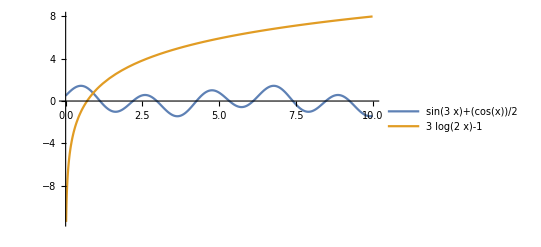

```mathematica
Plot[{f[x],g[x]},{x,0,10}, PlotLegends -> {f[x],g[x]}]
```

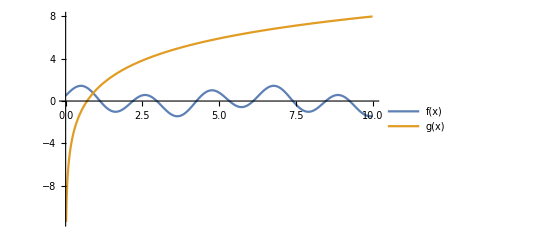

```mathematica
Plot[{f[x],g[x]},{x,0,10}, PlotLegends -> "Expressions"]
```

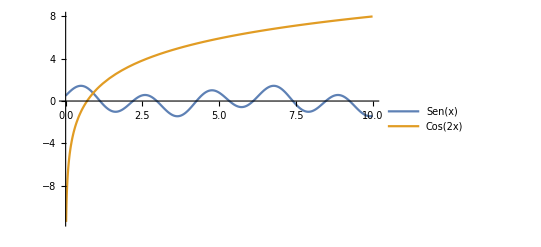

```mathematica
Plot[{f[x],g[x]},{x,0,10}, PlotLegends -> {"Sen(x)","Cos(2x)"}]
```

```mathematica
Plot[{f[x],g[x]},{x,0,10}, PlotLegends -> Placed[{f[x],g[x]},Below]]
```

-Graphics-

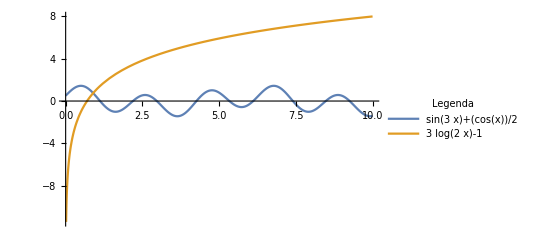

```mathematica
Plot[{f[x],g[x]},{x,0,10}, PlotLegends -> LineLegend[{f[x],g[x]},LegendLabel->"Legenda", LegendFunction->(Framed[#, RoundingRadius->5]&),LegendMargins->5]]
```

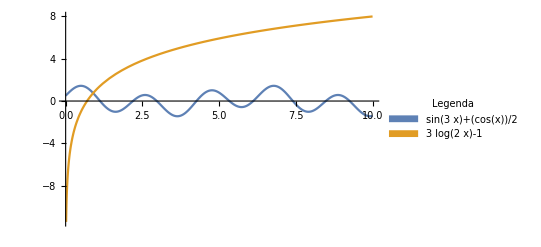

```mathematica
Plot[{f[x],g[x]},{x,0,10}, PlotLegends -> SwatchLegend[{f[x],g[x]},LegendLabel->"Legenda", LegendFunction->(Framed[#, RoundingRadius->5]&),LegendMargins->10]]
```

Exemplo Finalizado

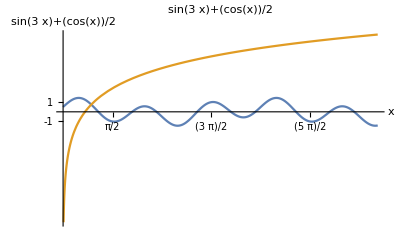

```mathematica
Plot[{f[x],g[x]},{x,0,10}, Ticks->{{Pi/2,2 Pi/2,3 Pi/2,4 Pi/2,5 Pi/2, 6 Pi/2},{-1,1}}, PlotLabel-> Style[Framed[f[x]],18, Blue],AxesLabel->{x,f[x]}, LabelStyle->Directive[Bold,Darker[Red],14],TicksStyle->Directive[Darker[Green],12], PlotLegends-> SwatchLegend[{f[x],g[x]}, LegendLabel->"Legenda", LegendFunction->(Framed[#, RoundingRadius->10]&)LegendMargins->5]]
```